Metody numeryczne, Informatyka NS sem. III, 2023/2024

# Projekt 6 – metoda Rungego-Kutty

Napisz program, który dla argumentów wejściowych:

f – funkcja rozwiązywanego równania różniczkowego y'=f(x,y),

a – początek przedziału,

b – koniec przedziału,

y0 – wartość z warunku początkowego,

n – liczba punktów węzłowych,

poszukiwał będzie (i porównywał ze sobą) rozwiązań zagadnienia Cauchy’ego y'=f(x,y), x∈[a,b], y(a)=y_0 metodami Rungego-Kutty rzędu 3 i 4. Program zwracał będzie dwa rysunki. Na pierwszym znajdować się będą wykresy rozwiązania dokładnego (linia ciągła), rozwiązania uzyskanego metodą Rungego-Kutty rzędu 3 (czerwone punkty) i rozwiązania uzyskanego metodą Rungego-Kutty rzędu 4 (zielone punkty). Na drugim wykresie będą przedstawione błędy bezwzględne obu metod (kolory jak poprzednio).
Wskazówka: rozwiązanie dokładne można uzyskać dzięki poleceniu: DSolve[{y’[x]==f[x,y[x]],y[a]==y0},y[x],x]⟦1,1,2⟧

## Przykłady

### Przykład 1.

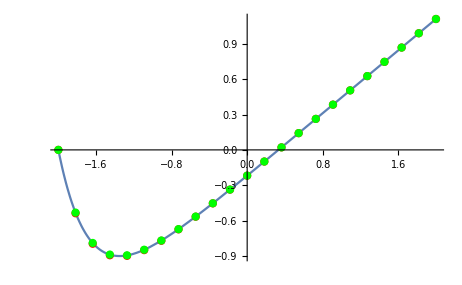
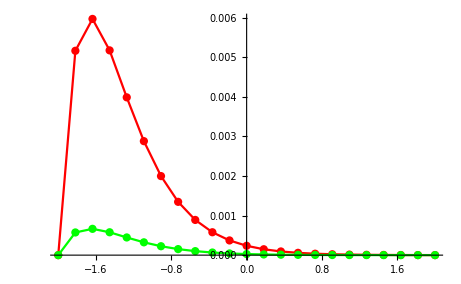
f[x_,y_]:=2x-3y;
rk3RK4[f,-2,2,0,23]
-Graphics-
-Graphics-

### Przykład 2.

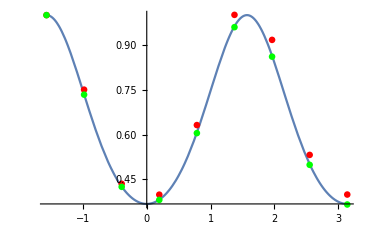
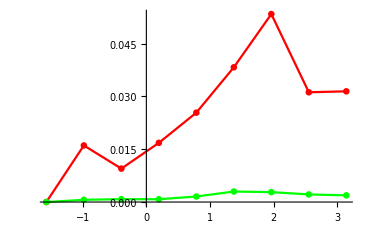
f[x_]:=y Sin[2x];
rk3RK4[f,-Pi/2,Pi,1,9]
-Graphics-
-Graphics-

### Przykład 3.

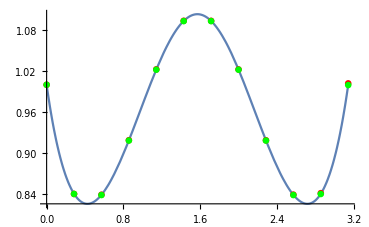
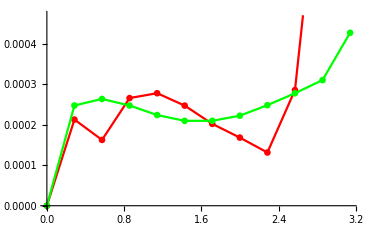
f[x_]:=y Sin[2x]-y y  Cos[x];
rk3RK4[f,0,Pi,1,12]
-Graphics-
-Graphics-

### Przykład 4.

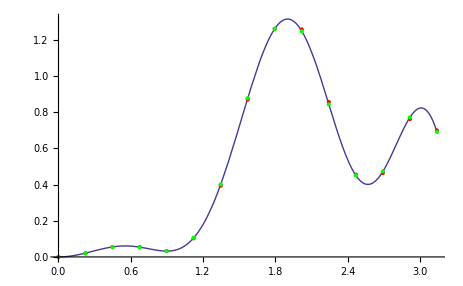
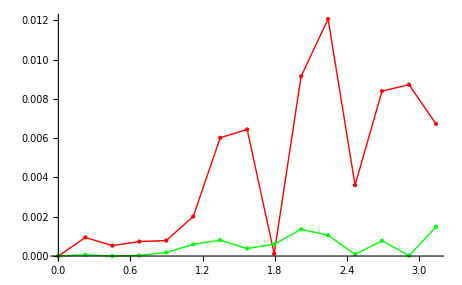
f[x_,y_]:=E^x Sin[x]Cos[2x]^2-3y;
rk3RK4[f,0,π,0,15]
-Graphics-
-Graphics-